## Uppgift 5

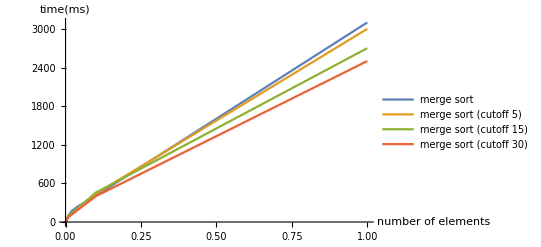

```mathematica
mergeSortTimes = {{100,0},{1000,1},{10000,8},{30000,17},{90000,97},{200000,169},{400000,240},{1000000,408}, {10000000,3100}};
mergeSortCUTOFF5 = {{10000,8},{90000,92},{1000000,436},{10000000,3000}};
mergeSortCUTOFF15 = {{10000,8},{90000,89},{1000000,456},{10000000,2700}};
mergeSortCUTOFF30 = {{10000,9},{90000,75},{1000000,400},{10000000,2500}};
ListLinePlot[{mergeSortTimes,mergeSortCUTOFF5,mergeSortCUTOFF15,mergeSortCUTOFF30}, AxesLabel->{"number of elements", "time(ms)"}, PlotLegends->{"merge sort","merge sort (cutoff 5)","merge sort (cutoff 15)","merge sort (cutoff 30)"}]
```

## DISCUSSION:

We see in the graph that applying a cutoff to insertion sort has its advantages. For smaller amounts of the attempt of optimizing the merge sort with a cutoff wasn’t that clear. 

This can be because every measurement uses different randomized lists, making it so that there is a scenario where the insertion sort part of the algorithm can get a worst case scenario, affecting the result. However we can see that when moving to larger amounts of data to be sorted the the optimized algorithms starts to pull ahead. This is not entirely unreasonable since insert sort has a good best case and a really bad worst case, making it so that if we add it to parts of the merge sort it can give varied best and worst cases for the combined algorithm.